# VE401 Recitation 6

## Single Sample Tests and Comparison of Parameter

### Test Statistics

From now on, you will learn a lot of tests. For each test, you need to pay attention to:

What parameter are we testing?

What parameter do we know?

What is the distribution of test statistics?

Denoting the distribution of test statistics as 𝒟, and 𝒹_α as the number such that ∫_(-∞)^𝒹_α f_𝒟(x)ⅆx=1-α, we reject at significance level α,

H_0:θ=θ_0 if 𝒟>𝒹_(α/2) or 𝒟<𝒹_(1-α/2). (Test statistics is too small or too big)

H_0:θ≤θ_0 if 𝒟>𝒹_α. (Test statistics is too big)

H_0:θ≥θ_0 if 𝒟<𝒹_(1-α). (Test statistics is too small)

### Single Sample Tests for Mean (Z-Test and T-Test)

Testing 
Parameter | Distribution of X_i | Variance  σ | Sample Size n | Test Statistics | OC Curve x-axis
(for two sided test)
μ | normal | known | any | Z=(X̄-μ_0)/(σ/√n) | d=(|μ-μ_0|)/σ
 | any | known | large |  | 
 | any | unknown | large | Z=(X̄-μ_0)/(S/√n) | d=(|μ-μ_0|)/S
 | normal | unknown | small | T_(n-1)=(X̄-μ_0)/(S/√n) |

Example:

##### If the true variance is unknown, what is the power of my T-test if the true mean is μ=499ml?

```mathematica
(500-499)/(√Variance[Data])
```

0.462933

The corresponding power is about 1-0.35=0.65.

### Single Sample Tests for Variance (Chi-Squared Test)

Testing Parameter | Distribution of X_i | Test Statistics | OC Curve x-axis
(for two sided test)
σ | Normal | χ_(n-1)^2=((n-1)S^2)/σ_0^2 | λ=σ/σ_0

### Single Sample Tests for Median (Non-Parametric)

#### Sign Test for the Median

Testing Parameter | Distribution of X_i | Test Statistics
M | any | Binomial_(n,0.5)=Q_+

where Q_+ is the number of data that lies above M_0. (Usually the data equal to M_0 is discarded).

Example:

```mathematica
Data
```

{499.728,497.006,498.871,500.931,500.157,501.139,495.516,501.89,496.894,497.132,503.624,500.357,498.011,498.447,496.074,502.177,498.081,499.719,497.657,498.895}

##### Test the hypothesis H_0:M≥500ml.

We can count that Q_+=7. P[Q_+≤7]=1/2^20∑_(i=0)^7 (20
i)=0.13. There is no enough evidence to reject H_0.

#### Wilcoxon Signed Rank Test

Testing Parameter | Distribution of X_i | Test Statistics
M | symmetric | W_+

where W_+ is the sum of the positive ranks when ranking |X_i-M_0|. When there is a tie, we take the average value. For example, if the first, second and third smallest |X_i-M_0|  is a group of 3 ties, we rank them all as (1+3)/2=2.
For small n, you can refer to a table of critical values here: http://users.stat.ufl.edu/~winner/tables/wilcox_signrank.pdf. For n≥10, we can approximate the test statistics with E[W]=(n(n+1))/4, Var[W]=(n(n+1)(2n+1))/24. For each group of t ties, the variance is reduced by (t^3-t)/48.

```mathematica
Sort[Data-500]
```

{-4.48438,-3.92626,-3.10595,-2.9944,-2.86761,-2.34263,-1.98916,-1.91898,-1.55252,-1.12854,-1.1048,-0.281418,-0.271902,0.156908,0.356726,0.930833,1.13896,1.89039,2.17724,3.62415}

##### Test the hypothesis H_0:M≥500ml.

We can count that W_+=1+4+5+8+10+13+18=59. According to the table, the critical value for α=0.05 is 60. Since 59<60 we are able to reject H_0 with P<0.05.

```mathematica
Needs["HypothesisTesting`"]
SignedRankTest[Data,500,"TestDataTable",AlternativeHypothesis->"Less"]
```

| Statistic | P-Value
Signed-Rank | 59. | 0.0446939

### Estimation of Proportion

For a Bernoulli random variable X_i, we can calculate p̂=X̄=1/n∑_(i=1)^n x_i. The confidence interval for p would be

p̂±z_(α/2)√(p̂(1-p̂)/n)

If we want to test that |p-p̂|<d for some d>0 with 100(1-α)% confidence, we need the sample size to be at least

n=(z_(α/2)^2 p̂(1-p̂))/d^2≤(z_(α/2)^2)/(4 d^2)

Example:

```mathematica
Data
```

{499.728,497.006,498.871,500.931,500.157,501.139,495.516,501.89,496.894,497.132,503.624,500.357,498.011,498.447,496.074,502.177,498.081,499.719,497.657,498.895}

##### Give a 95% confidence interval of the proportion of good product (with volume ≥500ml) in my batch.

We have p̂=7/20=0.35 and n=20. A confidence interval would be 0.35±0.21.

### Single Sample Test of Proportion (Z-Test)

According to central limit theorem, p̂ is approximately normally distributed with mean p and variance p(1-p)/n.

Testing Parameter | Distribution of X_i | Sample Size | Test Statistics
p | Bernoulli | large | Z=(p̂-p_0)/(√(p_0(1-p_0)/n))

### Comparing Two Proportions (Z-Test, Pooled Test)

Testing Parameter | Distribution of X_i | Sample Size | Hypothesis H_0 | Test Statistics
p_1-p_2 | Bernoulli | large | |p_1-p_2|≥d
for some d>0 | Z=((p̂)_1-(p̂)_2-(p_1-p_2)_0)/(√(((p̂)_1(1-(p̂)_1))/n_1+((p̂)_2(1-(p̂)_2))/n_2))
 |  |  | p_1=p_2 | Z=((p̂)_1-(p̂)_2)/(√(p̂(1-p̂)(1/n_1+1/n_2)))
where p̂=(n_1(p̂)_1+n_2(p̂)_2)/(n_1+n_2)

### F Distribution

Purpose: To describe the distribution of the ratio of two scaled chi-squared random variables.

Mathematical representation: F_(γ_1,γ_2)=(χ_γ_1^2/γ_1)/(χ_γ_2^2/γ_2)is said to follow an F-distribution with γ_1 and γ_2 degrees of freedom.

Properties:

P[F_(γ_1,γ_2)<x]=1-P[F_(γ_2,γ_1)<1/x].

f_(1-α,γ_1,γ_2)=1/(f_(α,γ_2,γ_1)).

```mathematica
P[1/x<F<x]=P[F<x]-P[F<1/x]=P[F<x]-
```

```mathematica
CDF[FRatioDistribution[4,5],1]
```

BetaRegularized[4/9,2,5/2]

### Comparing Two Variance (F-Test)

Testing Parameter | Distribution of X_i | Test Statistics | Hypothesis H_0 | OC Curve x-axis
(forn_1=n_2=n)
σ_1/σ_2 | Normal | F_(n_1-1,n_2-1)=S_1^2/S_2^2 | σ_1/σ_2≥1
σ_1/σ_2≤1
σ_1/σ_2=1 | λ=σ_1/σ_2

Example:

##### Plot the OC Curve For F-test for sample sizes n_1, n_2.

P[fail to reject H_0]=P[Sample statistics lies outside critical region]
=P[f_(0.975,n_1-1,n_2-1)<S_1^2/S_2^2<f_(0.025,n_1-1,n_2-1)|λ=σ_1/σ_2]
=P[(1/σ_1^2)/(1/σ_2^2)f_(0.975,n_1-1,n_2-1)<(S_1^2/σ_1^2)/(S_2^2/σ_2^2)<(1/σ_1^2)/(1/σ_2^2)f_(0.025,n_1-1,n_2-1)|λ=σ_1/σ_2]
=P[1/λ^2 f_(0.975,n_1-1,n_2-1)<(S_1^2/σ_1^2)/(S_2^2/σ_2^2)<1/λ^2 f_(0.025,n_1-1,n_2-1)|λ=σ_1/σ_2]
=P[1/λ^2 f_(0.975,n_1-1,n_2-1)<F_(n_1-1,n_2-1)<1/λ^2 f_(0.025,n_1-1,n_2-1)]

One nice property for this β=f(λ) curve is f(λ)=f(1/λ).

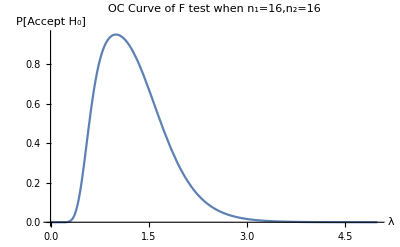

```mathematica
Subscript[n, 1]=16;Subscript[n, 2]=16;
f[λ_]:=CDF[FRatioDistribution[Subscript[n, 1]-1,Subscript[n, 2]-1],1/λ^2 InverseCDF[FRatioDistribution[Subscript[n, 1]-1,Subscript[n, 2]-1],0.975]]-CDF[FRatioDistribution[Subscript[n, 1]-1,Subscript[n, 2]-1],1/λ^2 InverseCDF[FRatioDistribution[Subscript[n, 1]-1,Subscript[n, 2]-1],0.025]];
Plot[f[λ],{λ,0,5},PlotLabel->"OC Curve of F test when n_1="<>ToString[Subscript[n, 1]]<>",n_2="<>ToString[Subscript[n, 2]],AxesLabel->{"λ","P[Accept H_0]"}]
```

### Comparing Two Means (Z-test, Pooled/Paired T-test)

Example: I am a soft drink manufacturer and I have two machines that produce bottles of soft drink. I would like to know if there is a difference in the products of the two machines. I sampled 10 bottles from each of the two machines.

```mathematica
Data1=RandomVariate[NormalDistribution[499,2],10]
Data2=RandomVariate[NormalDistribution[500,2],10]
```

{500.225,497.209,502.43,499.553,498.25,498.235,498.463,496.606,498.849,498.312}

{500.439,497.685,498.616,499.87,501.796,500.566,499.231,497.896,499.774,498.836}

```mathematica
Mean[Data1]
Mean[Data2]
```

498.813

499.471

```mathematica
√Variance[Data1]
√Variance[Data2]
```

1.63617

1.27599

I would like to test H_0:μ_1≥μ_2, and H_1:μ_1≤μ_2-1.

Testing 
Parameter | Distribution 
of the two RVs | Sample size
n_1,n_2 | Variance
σ_1^2, σ_2^2 | Test Statistics | OC curve x-axis
(for two-tailed test)
μ_1-μ_2 | Normal | any | known | Z=((X̄)_1-(X̄)_2-(μ_1-μ_2)_0)/(√(σ_1^2/n_1+σ_2^2/n_2)) | d=(|μ_1-μ_2|)/(√(σ_1^2+σ_2^2)) where
n=(σ_1^2+σ_2^2)/(σ_1^2/n_1+σ_2^2/n_2)
 |  | large | unknown | Z=((X̄)_1-(X̄)_2-(μ_1-μ_2)_0)/(√(S_1^2/n_1+S_2^2/n_2)) | 
 |  | small | unknown with
σ=σ_1=σ_2 | T_(n_1+n_2-2)=((X̄)_1-(X̄)_2-(μ_1-μ_2)_0)/(√(S_p^2(1/n_1+1/n_2)))
where S_p^2=((n_1-1)S_1^2+(n_2-1)S_2^2)/(n_1+n_2-2) | In case of n=n_1=n_2, 
d=(|μ_1-μ_2|)/(2σ)
where we use modified 
sample size n^*=2n-1,
and σ can be estimated.
 |  | small | unknown | T_γ=((X̄)_1-(X̄)_2-(μ_1-μ_2)_0)/(√(S_1^2/n_1+S_2^2/n_2)) where
γ=((S_1^2/n_1+S_2^2/n_2)^2)/(((S_1^2/n_1)^2)/(n_1-1)+((S_2^2/n_2)^2)/(n_2-1)) (we take
the floor) | No simple OC Curves

##### Suppose I know that σ_1=σ_2=2, which test would you use? What is the test statistics?

The Z-test with known variance. The test statistics is Z=((X̄)_1-(X̄)_2-(μ_1-μ_2)_0)/(√(σ_1^2/n_1+σ_2^2/n_2))=(498.813-499.471)/(√(8/10))=-0.73. This gives us a P-value of 0.23. This is large, so we failed to reject H_0.

```mathematica
CDF[NormalDistribution[],(Mean[Data1]-Mean[Data2])/(√(8/10))]
```

0.230966

##### Suppose we don’t know about the true variance, but suppose we know they are equal. which test would you use? What is the test statistics?

The T-test with equal variance. We have pooled variance S_p^2=((n_1-1)S_1^2+(n_2-1)S_2^2)/(n_1+n_2-2)=(9(1.64)^2+9(21.28)^2)/18=2.15, so the test statistics is T_(10+10-2)=((X̄)_1-(X̄)_2-(μ_1-μ_2)_0)/(√(S_p^2(1/n_1+1/n_2)))=(498.813-499.471)/(√(2.15×2/19))=-1.0. This gives us a P-value of 0.16. So there is no evidence to reject H_0.

```mathematica
CDF[StudentTDistribution[18],(Mean[Data1]-Mean[Data2])/(√((Variance[Data1]+Variance[Data2])/2 2/10))]
```

0.1646152521384

```mathematica
√Variance[Data1]
√Variance[Data2]
```

1.63617

1.27599

##### Suppose we know that μ_1=499,μ_2=500. What is the power of the T-test for unknown variance if α=0.05?

We can use the estimated variance S_p^2=2.15, and calculate d=(μ_2-μ_1)/(2σ)≈1/(2 √2.15)=0.34. Choosing n^*=2n-1=19≈20, we get a β of approximately 0.56, so the power is approximately 0.44.

##### Suppose we don’t know anything about the true variance. which test would you use? What is the test statistics?

Welch’s T-test with unknown variance. We have the degrees of freedom γ=⌊((S_1^2/n_1+S_2^2/n_2)^2)/(((S_1^2/n_1)^2)/(n_1-1)+((S_2^2/n_2)^2)/(n_2-1))⌋=16. T_16=((X̄)_1-(X̄)_2-(μ_1-μ_2)_0)/(√(S_p^2(1/n_1+1/n_2)))=-1.0. This gives us again a P-value of 0.17. So there is no evidence to reject H_0.

```mathematica
Floor[(Variance[Data1]/10+Variance[Data2]/10)^2/((Variance[Data1]/10)^2/9+(Variance[Data2]/10)^2/9)]
```

16

### Comparing Locations (Non-parametric)

Testing Parameter | Distribution of X,Y | Sample Size | Hypothesis H_0 | Test Statistics
P[X>Y] | continuous | m samples of X
n samples of Y
m≤n. | P[X>Y]=1/2
P[X>Y]≥1/2
P[X>Y]≤1/2 | W_m

where W_m is the sum of ranks of X_1,...,X_m when we rank the samples X_1,...,X_m,Y_1,...,Y_n from the smallest to the largest. When there is a tie, we take the average value. For example, if the first, second and third smallest value is a group of 3 ties, we rank them all as (1+3)/2=2.
For small n, you can refer to a table of critical values here: https://www.stat.auckland.ac.nz/~wild/ChanceEnc/Ch10.wilcoxon.pdf. For n≥20, we can approximate the test statistics with normal distribution with E[W]=(m(m+n+1))/2, Var[W]=(mn(m+n+1))/12. If there are many ties, then for each group of t ties, the denominator of variance is reduced by (t^3+t)/12.

```mathematica
PairedHistogram[Data1,Data2,ChartLegends->{{"Machine 1","Machine 2"}},ChartStyle->{"Pastel",None,None}]
```

-Graphics-

```mathematica
Sort[Data1]
```

{496.606,497.209,498.235,498.25,498.312,498.463,498.849,499.553,500.225,502.43}

```mathematica
Sort[Data2]
```

{497.685,497.896,498.616,498.836,499.231,499.774,499.87,500.439,500.566,501.796}

##### Use Wilcoxon Rank Sum test to test the hypothesis H_0:P[X>Y]≥1/2.

The test statistics W_m=1+2+5+6+7+8+11+13+16+20=89. From the table, we can see that the P-value lies between 0.1 and 0.2. There is no strong evidence to reject P[X>Y]≥1/2.

### Test for Mean of Difference of two RVs (Paired T-test)

For our data, we can say: we do 10 times of sampling. For each sampling, we take one sample each from the two machines. We can pair the data and get a new data D_i:=X_i-Y_i.

```mathematica
d=Data1-Data2
```

{-0.213956,-0.476581,3.8135,-0.317297,-3.54625,-2.33138,-0.768637,-1.29035,-0.925138,-0.523963}

```mathematica
Mean[d]
Variance[d]
```

-0.658004

3.55379

Testing Parameter | Distribution of (X,Y) | Sample Size | Test Statistics
μ_D
where D=X-Y | joint bivariate
normal distribution | n=n_X=n_Y | T_(n-1)=(D̄-(μ_D)_0)/(√(S_D^2/n))
M_D
where  D=X-Y | independent, same distribution
but different location (D symmetric) | any | W_+ (Wilcoxon
signed rank statistics)

##### Test H_0:μ_D≥0 using paired T-test.

We have T_(n-1)=(D̄-(μ_D)_0)/(√(S_D^2/n))=-0.65/(√(3.55/10))=-1.10. The P-value is then 0.15. We don’t have enough evidence to reject H_0.

```mathematica
CDF[StudentTDistribution[9],Mean[d]/(√(Variance[d]/10))]
```

0.1491623448998

Recall that the pooled T-test gives us a P-value of 0.17. In general, pairing with the absence of correlation is unnecessary and actually makes a test less powerful.

### Comparison Between Pooled and Paired T-test

If n_X=n_Y=n, we can use both

Testing Parameter | Distribution of (X,Y) | Test Statistics
μ_X-μ_Y | joint bivariate
normal distribution
 | T_(2n-2)=(X̄-Ȳ)/(√(2S_p^2/n))    where S_p^2=(S_1^2+S_2^2)/2
 |  | T_(n-1)=(D̄-(μ_D)_0)/(√(S_D^2/n))

```mathematica
Manipulate[
Plot[{PDF[StudentTDistribution[Floor[γ]],x],PDF[NormalDistribution[],x]},{x,-5,5},
PlotRange->{0,0.5},
Filling->Bottom,
AxesLabel->{"x","f_X(x)" },
PlotLabel->"PDF of Student T Distribution with γ="<>ToString[Floor[γ]],
PlotLegends->{"Student T Distribution","Standard Normal"}
],{γ,1,20},
Paneled->False]
```

When the test statistics is the same, pooled T-test is more powerful because of more degrees of freedom.

We have S_D^2/n≈σ_(D̄)^2=(2 σ^2)/n(1-ρ_XY)≈(2 S_p^2)/n(1-ρ_XY). So, when n is large enough (so that difference in degrees of freedom has less impact), polled T-test will have Piecewise[{{smaller power, if ρ_XY>0}, {larger power, if ρ_XY≤0}}].

### Estimation of Correlation Coefficient

We use method of moments to get an estimator for ρ_XY:

R=ρ̂=(∑(X_i-X̄)(Y_i-Ȳ))/(√(∑(X_i-X̄)^2)√(∑(Y_i-Ȳ)^2))

### Single Sample Test for Correlation Coefficient (Z-test)

Testing Parameter | Sample Size | Test Statistics
ρ | large |  Z=(√(n-3))/2 (ln((1+R)/(1-R))-ln((1+ρ_0)/(1-ρ_0)))=√(n-3)(artanh(R)-artanh(ρ_0))

The 100(1-α)% confidence interval for ρ is tanh(artanh(R)±(z_(α/2))/(√(n-3)))

##### Calculate a 95% confidence interval of the correlation coefficient between the bottle volumes produced by the two machines.

```mathematica
Covariance[Data1,Data2]/(√(Variance[Data1]Variance[Data2]))
```

0.179961

We have R=(∑(X_i-X̄)(Y_i-Ȳ))/(√(∑(X_i-X̄)^2)√(∑(Y_i-Ȳ)^2))=0.180. 
Then tanh(artanh(R)±(z_(α/2))/(√(n-3)))=tanh(0.180±0.741)=[-0.51,0.73].

```mathematica
Tanh[ArcTanh[Covariance[Data1,Data2]/(√(Variance[Data1]Variance[Data2]))]+InverseCDF[NormalDistribution[],1-0.025]/(√7)]
```

0.727191

## Categorical Data

### Multinomial Distribution

A multinomial trial with parameter p_1,...,p_k is a trial that can result in one of k outcomes, with the probability of getting i^th outcome is p_i. 
We define random vector (X_1,...,X_k):S→Ω={0,1,...,n}^k and PDF f_(X_1 X_2... X_k)(x_1,...,x_k)=(n!)/(x_1!...x_k!)p_1^x_1... p_k^x_k to have a multinomial distribution with parameters n and p_1,...,p_k.

Properties:

For i=1,...,k, E[X_i]=n p_i,

Var[X_i]=n p_i(1-p_i).

For 1≤i<j≤k, Cov[X_i,X_j]=-n p_i p_j.

### Pearson Statistics

Let ((X_1,...,X_k),f_(X_1 X_2... X_k)(x_1,...,x_k)) be multinomial random variable with parameters n and p_1,...,p_k. For large n,

∑_(i=1)^k (X_i-n p_i)^2/(n p_i)=∑_(i=1)^k (X_i-E[X_i])^2/E[X_i]=:∑_(i=1)^k (O_i-E_i)^2/E_i

follows an approximate chi-squared distribution with k-1 degrees of freedom. Here O_i is the observed value and E_i is the expected value. For the approximation we require

E[X_i]=n p_i≥1 | for all i=1,...,k
E[X_i]=n p_i≥5 |                 for 80% of all i=1,...,k

### Chi-Squared Goodness-of-Fit Test

Purpose: To fit a distribution on the data.

Testing Parameter | Sample Size | Test Statistics
p_1,...,p_k | large | X_(k-1-m)^2 =∑_(i=1)^k (O_i-E_i)^2/E_i
where k is the number of categories
and m is number of parameters we estimate

If the test statistics is too large (X_(k-1-m)^2 >χ_(α,k-1-m)^2), we reject H_0:p_i=p_i_0.

#### Goodness-of-Fit Test for Discrete Distribution

Steps:

Usually in discrete distribution case, the categories are set.

Calculate the expected value for each category given hypothesis is true. Sometimes the categories is incomplete, e.g. {0,1,2,3,4,5}⊂ℕ. In this case the boundary category should also cover the probability that the value is greater than itself. Namely we need to calculate P[X=0],...,P[X=4],P[X≥5].

Determine degrees of freedom.

Calculate critical region.

Calculate Pearson statistics to see if we can reject H_0.

##### Raindrops keep falling on my head at an unknown rate. I record the number of raindrops that fall on my head in every minute, and found that in a 42 minute time period, Raindrops per minute | no. of minutes | p_i | E_i 0 | 3 | | 1 | 14 | | 2 | 9 | | 3 | 7 | | 4 | 5 | | 5 | 4 | | . (1) Suppose this is a Poisson distribution with parameter k, what is the estimation of k? (2) Test whether this is a Poisson distribution with parameter k̂. (3) Is this a proper categorization? What is the degree of freedom of test statistics?

Suppose this is a Poisson distribution, then we have k̂=X̄=(0×3+1×14+2×9+3×7+4×5+5×4)/42=2.21. Then we calculate the expected value for each category. For example for X=0, P[X=0]=(e^-2.21 2.21^0)/(0!)=0.11, so E_i=42P[X=0]=4.6.

```mathematica
dist=PoissonDistribution[2.21];
Grid[{{Null,0,1,2,3,4,"5 or more"},Prepend[42 Append[Table[N[PDF[dist,x]],{x,0,4}],N[Probability[x≥5,x\[Distributed]dist]]],"Expected"],{"Observed",3,14,9,7,5,4}}]
```

| 0 | 1 | 2 | 3 | 4 | 5 or more
Expected | 4.60743 | 10.1824 | 11.2516 | 8.28865 | 4.57948 | 3.09045
Observed | 3 | 14 | 9 | 7 | 5 | 4

And we found that this violates the Cochran’s rule, so we adjust to merge the last two categories:

```mathematica
Grid[{{Null,0,1,2,3,"4 or more"},Prepend[42 Append[Table[N[PDF[dist,x]],{x,0,3}],N[Probability[x≥4,x\[Distributed]dist]]],"Expected"],{"Observed",3,14,9,7,5+4}}]
```

| 0 | 1 | 2 | 3 | 4 or more
Expected | 4.60743 | 10.1824 | 11.2516 | 8.28865 | 7.66994
Observed | 3 | 14 | 9 | 7 | 9

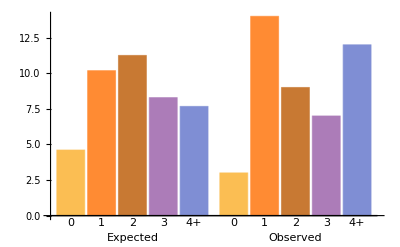

```mathematica
BarChart[{42 Append[Table[N[PDF[dist,x]],{x,0,3}],N[Probability[x≥4,x\[Distributed]dist]]],{3,14,9,7,12}},ChartLabels->{{"Expected","Observed"},{"0","1","2","3","4+"}}]
```

This time it’s good. The test statistics is then

χ_(5-1-1)^2=(4.61-3)^2/4.61+(10.18-14)^2/10.18+(11.25-9)^2/11.25+(8.29-7)^2/8.29+(7.67-9)^2/7.67
=2.877

The critical value is

```mathematica
InverseCDF[ChiSquareDistribution[3],0.95]
```

7.81473

Since 2.877<7.81, we cannot reject H_0:The data follows Poisson distribution with k=2.21.

#### Goodness-of-Fit Test for Continuous Distribution

Steps:

Usually in continuous distribution case, you need to set the categories. This is by dividing ℝ into k equally likely segments. e.g. For normal distribution and k=8,

(a_0,a_1)=(-∞,-1.15),[a_1,a_2)=[-1.15,-0.675),[a_2,a_3)=[-0.675,-0.32),[a_3,a_4)=[-0.32,0)
[a_4,a_5)=[0,0.32),[a_5,a_6)=[0.32,0.675),[a_6,a_7)=[0.675,1.15),[a_7,a_8)=[1.15,∞)

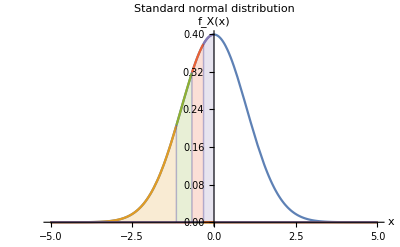

```mathematica
Plot[{PDF[NormalDistribution[],x],Piecewise[{{PDF[NormalDistribution[],x],x<-1.15}}],Piecewise[{{PDF[NormalDistribution[],x],-1.15≤x<-0.675}}],Piecewise[{{PDF[NormalDistribution[],x],-0.675≤x<-0.32}}],Piecewise[{{PDF[NormalDistribution[],x],-0.32≤x<0}}]},{x,-5,5},PlotRange->All,Filling->{2->Axis,3->Axis,4->Axis,5->Axis},PlotLabel->"Standard normal distribution",AxesLabel->{"x","f_X(x)"}]
```

Calculate the expected value for each category, which should be n/k for every category. Categorize your data according to those intervals to get the observed values.

Determine degrees of freedom.

Calculate critical region.

Calculate Pearson statistics to see if we can reject H_0.

#### Independence of Categorizations

Testing Parameter | Sample Size | Test Statistics
p_1,...,p_k | large | X_((r-1)(c-1))^2 =∑_(i=1)^r ∑_(i=1)^c (O_ij-E_ij)^2/E_ij
where r is the number of rows
and c is the number of columns

Steps:

Sum the rows and columns to get the marginal row and column sums n_(i·),n_(·j). These are used to estimate marginal densities (p̂)_(i·)=(n_(i·))/n,(p̂)_(·j)=(n_(·j))/n.

For each grid (i,j), multiply the estimated marginal densities together and calculate the expected number E_ij=(n_(i·)n_(·j))/n.

Determine degrees of freedom.

Calculate critical region.

Calculate Pearson statistics to see if we can reject H_0.

##### We conducted a survey. In the survey, people are asked to fill in their gender and age. It is shown as follows: | Male | | Female | | n_(i·) | O_i | E_i | O_i | E_i | Under 18 | 75 | | 25 | | 18 to 29 | 1242 | | 60 | | 30 to 50 | 1531 | | 68 | | above 50 | 1040 | | 39 | | n_(·j) | | | | | . Are the age and gender of participants independent?

| Male |  | Female |  | n_(i·)
 | O_i | E_i | O_i | E_i | 
Under 18 | 75 | 95.29 | 25 | 4.706 | 100
18 to 29 | 1242 |  1241 | 60 |  61.27 |  1302
30 to 50 | 1531 |  1524 | 68 |  75.25 |  1599
above 50 | 1040 |  1028 | 39 |  50.78 |  1079
n_(·j) |  3888   |  | 192    |  |  4080

Calculating the test statistics, X_((r-1)(c-1))^2 =∑_(i=1)^r ∑_(i=1)^c (O_ij-E_ij)^2/E_ij=95.34. The degrees of freedom is (r-1)(c-1)=3. The test statistics is far larger than the critical value, so we reject the null hypothesis that the gender and age are independent.

## Problems in Assignments

### Testing Hypotheses on an Exponential Variable

Let X be an exponential random variable with parameter β. Devise a test statistic for testing H_0:β=β_0 and H_0:β≤β_0.

#### Solution

We know that Y=X_1+...+X_n follows a Gamma distribution with α=n and β, so,

m_Y(t)=(1-t/β)^-n⇒m_(2β Y)(t)=m_Y(2β t)=(1-2 t)^-n

which is a moment generating function of Chi-squared distribution with γ=2n. So we conclude that 2β Y=2β∑_(i=1)^n X_i=2n β X̄ follows Chi-squared distribution with γ=2n. Therefore we set our test statistics to be X_(2n)^2=2n β_0 X̄ . 
We note that when the true β is larger, X̄, which is the estimator for the mean 1/β, will be smaller. So we reject

H_0:β=β_0 if X_(2n)^2>χ_(0.025,2n)^2 or X_(2n)^2<χ_(0.975,2n)^2.

H_0:1/β≥1/β_0 if X_(2n)^2<χ_(1-0.05,2n)^2.

### OC Curve For F-test

Calculate the power of F-test when n_1≠n_2.

#### Solution

P[fail to reject H_0]=P[Sample statistics lies outside critical region]
=P[f_(0.975,n_1-1,n_2-1)<S_1^2/S_2^2<f_(0.025,n_1-1,n_2-1)|λ=σ_1/σ_2]
=P[(1/σ_1^2)/(1/σ_2^2)f_(0.975,n_1-1,n_2-1)<(S_1^2/σ_1^2)/(S_2^2/σ_2^2)<(1/σ_1^2)/(1/σ_2^2)f_(0.025,n_1-1,n_2-1)|λ=σ_1/σ_2]
=P[1/λ^2 f_(0.975,n_1-1,n_2-1)<(S_1^2/σ_1^2)/(S_2^2/σ_2^2)<1/λ^2 f_(0.025,n_1-1,n_2-1)|λ=σ_1/σ_2]
=P[1/λ^2 f_(0.975,n_1-1,n_2-1)<F_(n_1-1,n_2-1)<1/λ^2 f_(0.025,n_1-1,n_2-1)]

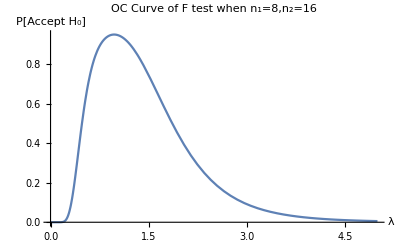

```mathematica
Subscript[n, 1]=8;Subscript[n, 2]=16;
f[λ_]:=CDF[FRatioDistribution[Subscript[n, 1]-1,Subscript[n, 2]-1],1/λ^2 InverseCDF[FRatioDistribution[Subscript[n, 1]-1,Subscript[n, 2]-1],0.975]]-CDF[FRatioDistribution[Subscript[n, 1]-1,Subscript[n, 2]-1],1/λ^2 InverseCDF[FRatioDistribution[Subscript[n, 1]-1,Subscript[n, 2]-1],0.025]];
Plot[f[λ],{λ,0,5},PlotLabel->"OC Curve of F test when n_1="<>ToString[Subscript[n, 1]]<>",n_2="<>ToString[Subscript[n, 2]],AxesLabel->{"λ","P[Accept H_0]"}]
```